```mathematica
link=Install[LinkConnect[" 40787@192.168.150.128,40471@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,ΩO=1/16,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbO=0.01125,ωbp=15*Sqrt[0.45],ωbO=3.75*Sqrt[0.45],ωe=150,
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,ΩO},{ωbp,ωe,ωbO},{θbp,θe,θbO}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=4.75,wna=88.25Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.97,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

```mathematica
sol=With[{k=Range[0.5,1.3,0.01],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[0.65,-0.00001] (1+0.0001 I {0,1,2}),MaxIterations->100]];


ListLinePlot[Im[sol[[2,2]]]]
```

```mathematica
gama={};
with[{k=Range[81]},gama=Append[gama,Im[sol[[2,2,k]]]]];
Export["1.txt",gama];
```

{2.77427-0.017011 ⅈ,2.77174-0.0122657 ⅈ,2.77037-0.00619323 ⅈ,2.77102+0.0012618 ⅈ,2.7748+0.00944814 ⅈ,2.78222+0.0169445 ⅈ,2.79278+0.0225051 ⅈ,2.80572+0.0256795 ⅈ,2.82065+0.0265462 ⅈ,2.83757+0.0254521 ⅈ,2.85673+0.0231016 ⅈ,2.87804+0.0207195 ⅈ,2.90039+0.0192645 ⅈ,2.92256+0.0184346 ⅈ,2.96865+0.0159275 ⅈ,2.97211+0.0197536 ⅈ}

{2.77427-0.017011 ⅈ,2.77174-0.0122657 ⅈ,2.77037-0.00619323 ⅈ,2.77102+0.0012618 ⅈ,2.7748+0.00944814 ⅈ,2.78222+0.0169445 ⅈ,2.79278+0.0225051 ⅈ,2.80572+0.0256795 ⅈ,2.82065+0.0265462 ⅈ,2.83757+0.0254521 ⅈ,2.85673+0.0231016 ⅈ,2.87804+0.0207195 ⅈ,2.90039+0.0192645 ⅈ,2.92256+0.0184346 ⅈ,2.96865+0.0159275 ⅈ,2.97211+0.0197536 ⅈ,2.98256+0.0101757 ⅈ,2.99002+0.00212101 ⅈ,2.99168-0.00143413 ⅈ,2.99241-0.003202 ⅈ,2.99283-0.00430494 ⅈ,2.99309-0.00508407 ⅈ,2.99327-0.005677 ⅈ,2.99339-0.00615091 ⅈ,2.99348-0.00654349 ⅈ,2.99354-0.00687696 ⅈ,2.99357-0.00716594 ⅈ,2.99359-0.00742032 ⅈ,2.9936-0.00764712 ⅈ,2.9936-0.00785149 ⅈ,2.99359-0.00803727 ⅈ}

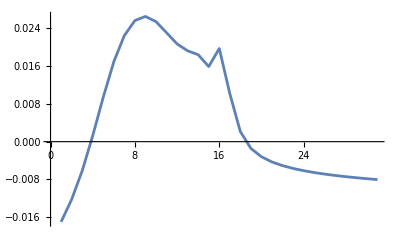

```mathematica
sol1=With[{k=Range[4.75,4.0,-0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[4.8,5.5,0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["oim88.csv",Im[sol]];

Export["re.csv",Re[sol]];
```